```mathematica
im=pgData["CEFI","Images","Swarm C","DateRange"->{{2022,1,22},{2022,1,23}}];
```

```mathematica
Length@im
```

1725

```mathematica
Manipulate[tiiImagePlot[im[[n]]],{n,1,Length@im,1}]
```

```mathematica
data=Transpose@Partition[im[[1394,1,3]],66];
```

```mathematica
Graphics[Raster[data,{{0,0},{40,66}},{0,1500},ColorFunction->"TemperatureMap"]]
```

-Graphics-

```mathematica
1024*768
```

786432

```mathematica
NotebookDirectory[]
```

/Users/john/src/tiim.dck/Mathematica/

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"../example/A20220121_001120.png"}]]
```

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"../example/SW_EFIA20220121_imaging_anomaly_stats.txt"}],"Table"]
```

{{secondsSince1970,PAH,PAV,MH,MV,CWH,CWV,BAH,BAV,UAWH,UAWV,LAWH,LAWV,UAX1H,UAX1V,UAY1H,UAY1V,UAX2H,UAX2V,UAY2H,UAY2V,LAX1H,LAX1V,LAY1H,LAY1V,LAX2H,LAX2V,LAY2H,LAY2V},1442,{1642745475,0,0,0,0,0,0,0,0,1,1,7,7.384,10.016,9.653,33.726,36.173,20.344,22.993,9.603,4.162,14.813,6.337}}
 |  |  |  |

```mathematica
vars=data[[1]];
TableForm[Transpose[{Range@Length@vars,vars}]]
```

1 | secondsSince1970
2 | PAH
3 | PAV
4 | MH
5 | MV
6 | CWH
7 | CWV
8 | BAH
9 | BAV
10 | UAWH
11 | UAWV
12 | LAWH
13 | LAWV
14 | UAX1H
15 | UAX1V
16 | UAY1H
17 | UAY1V
18 | UAX2H
19 | UAX2V
20 | UAY2H
21 | UAY2V
22 | LAX1H
23 | LAX1V
24 | LAY1H
25 | LAY1V
26 | LAX2H
27 | LAX2V
28 | LAY2H
29 | LAY2V

```mathematica
data1=data[[2;;]];
data1[[All,1]]=data1[[All,1]]+AbsoluteTime[{1970}];
```

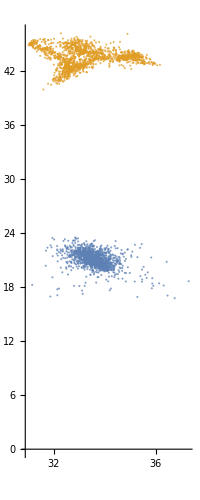

```mathematica
ListPlot[{data1[[All,{22,24}]]/.{x_,y_}:>{x,y},data1[[All,{14,16}]]/.{x_,y_}:>{x,y}},Joined->False,PlotStyle->Opacity[0.75],AspectRatio->Automatic]
```

```mathematica
DateListPlot[N@data1[[All,{1,11}]]]
```